```mathematica
initialDist={{0.194217,0.261392,0.170547,0.220699,0.107902,0.788033,0.749864,0.277985,0.905023,0.670611,0.950583,0.943787,0.0876439,0.0997864,0.640183,0.268341},{0.993959,0.113036,0.0484695,0.678111,0.0164464,0.0138953,0.216109,0.76302,0.767249,0.80132,0.827801,0.646148,0.264289,0.941546,0.422971,0.478734},{0.795924,0.626972,0.332627,0.451013,0.883308,0.671722,0.247665,0.659808,0.334717,0.883038,0.850722,0.0138388,0.376204,0.0994747,0.0923429,0.0842617},{0.0740472,0.817788,0.0707233,0.834878,0.585138,0.0609502,0.371949,0.850302,0.793159,0.885539,0.328632,0.826443,0.644193,0.879568,0.404873,0.707733},{0.404492,0.571416,0.159547,0.341449,0.0670355,0.849984,0.400274,0.0455545,0.979634,0.57656,0.00366479,0.470327,0.786076,0.822125,0.199412,0.124014},{0.878658,0.018935,0.73447,0.65637,0.565128,0.673553,0.787897,0.849004,0.0806247,0.0138632,0.379276,0.151241,0.902807,0.0763203,0.534992,0.517203},{0.97305,0.564265,0.862289,0.68262,0.719147,0.869007,0.571621,0.16744,0.895593,0.149874,0.789144,0.97825,0.901169,0.687881,0.441086,0.137905},{0.0595974,0.306073,0.590297,0.263187,0.144626,0.126185,0.187313,0.651824,0.609501,0.0852119,0.114096,0.905758,0.846465,0.968883,0.407452,0.429938},{0.398952,0.00781185,0.047606,0.943385,0.650109,0.770502,0.930246,0.223664,0.613198,0.00147594,0.152959,0.609634,0.687327,0.616106,0.357288,0.235187},{0.188067,0.904603,0.610194,0.381091,0.554067,0.944039,0.283008,0.153834,0.649562,0.0752809,0.264808,0.22996,0.839838,0.793354,0.278869,0.1147},{0.528653,0.865704,0.843372,0.867183,0.066855,0.516023,0.56376,0.0440568,0.983766,0.800711,0.831055,0.621157,0.495701,0.0979154,0.729266,0.415688},{0.745043,0.0761648,0.11827,0.913328,0.347903,0.518661,0.401349,0.181992,0.598214,0.189629,0.95553,0.0552998,0.164102,0.762727,0.558027,0.538557},{0.0465698,0.975362,0.290494,0.345015,0.474207,0.134516,0.669641,0.504087,0.461505,0.404736,0.391687,0.624677,0.676798,0.691767,0.864109,0.91592},{0.0170812,0.0696675,0.304805,0.62166,0.653715,0.747483,0.888248,0.302419,0.507434,0.793698,0.622194,0.233489,0.376977,0.897271,0.727222,0.843657},{0.930333,0.574546,0.907103,0.538488,0.160013,0.260363,0.933598,0.822927,0.413092,0.616379,0.822783,0.302201,0.342146,0.872191,0.87572,0.0340569},{0.320665,0.023777,0.617203,0.440015,0.862541,0.466339,0.383168,0.706456,0.408273,0.819805,0.162313,0.39144,0.827702,0.293227,0.0394612,0.947903}};

finalDist={{0.0138632,0.913328,0.767249,0.293227,0.149874,0.0138953,0.626972,0.0752809,0.676798,0.381091,0.97305,0.283008,0.0806247,0.624677,0.749864,0.850302},{0.649562,0.39144,0.0552998,0.883308,0.571416,0.793159,0.904603,0.413092,0.865704,0.0440568,0.822927,0.554067,0.930333,0.401349,0.0609502,0.304805},{0.144626,0.826443,0.233489,0.707733,0.347903,0.0994747,0.264808,0.558027,0.137905,0.616379,0.223664,0.00366479,0.152959,0.80132,0.585138,0.941546},{0.495701,0.0876439,0.613198,0.466339,0.846465,0.983766,0.687881,0.827702,0.334717,0.76302,0.888248,0.451013,0.659808,0.867183,0.371949,0.73447},{0.879568,0.671722,0.91592,0.153834,0.650109,0.407452,0.199412,0.047606,0.95553,0.400274,0.0670355,0.834878,0.302419,0.0763203,0.220699,0.0164464},{0.170547,0.0484695,0.379276,0.793698,0.277985,0.0740472,0.905023,0.517203,0.160013,0.670611,0.574546,0.124014,0.943787,0.538488,0.622194,0.404873},{0.518661,0.843372,0.590297,0.107902,0.872191,0.565128,0.817788,0.376204,0.850722,0.00147594,0.788033,0.260363,0.383168,0.719147,0.897271,0.793354},{0.651824,0.290494,0.944039,0.727222,0.341449,0.0170812,0.678111,0.0923429,0.621157,0.422971,0.901169,0.646148,0.839838,0.159547,0.0707233,0.235187},{0.023777,0.470327,0.164102,0.0595974,0.644193,0.194217,0.474207,0.883038,0.302201,0.189629,0.0842617,0.528653,0.0455545,0.441086,0.616106,0.862289},{0.1147,0.687327,0.869007,0.404736,0.827801,0.968883,0.747483,0.134516,0.571621,0.822783,0.691767,0.950583,0.22996,0.786076,0.975362,0.332627},{0.902807,0.56376,0.268341,0.610194,0.0979154,0.534992,0.264289,0.415688,0.930246,0.0340569,0.328632,0.598214,0.849984,0.376977,0.0138388,0.745043},{0.822125,0.181992,0.97825,0.770502,0.907103,0.00781185,0.864109,0.0761648,0.640183,0.516023,0.87572,0.0997864,0.478734,0.673553,0.151241,0.461505},{0.0852119,0.398952,0.0394612,0.345015,0.16744,0.65637,0.795924,0.320665,0.762727,0.162313,0.391687,0.789144,0.933598,0.278869,0.862541,0.617203},{0.306073,0.895593,0.669641,0.538557,0.878658,0.404492,0.113036,0.609501,0.0465698,0.905758,0.653715,0.018935,0.609634,0.066855,0.408273,0.947903},{0.787897,0.216109,0.831055,0.0696675,0.247665,0.729266,0.849004,0.979634,0.440015,0.263187,0.843657,0.504087,0.188067,0.819805,0.126185,0.68262},{0.564265,0.11827,0.429938,0.62166,0.943385,0.507434,0.342146,0.187313,0.800711,0.57656,0.114096,0.706456,0.885539,0.357288,0.993959,0.261392}};
```

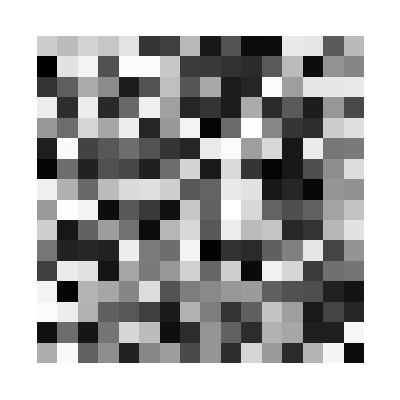

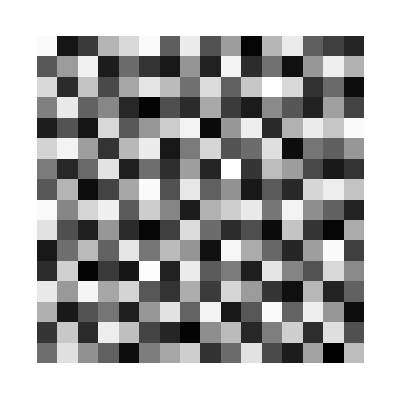

```mathematica
ArrayPlot[initialDist]
ArrayPlot[finalDist]
```

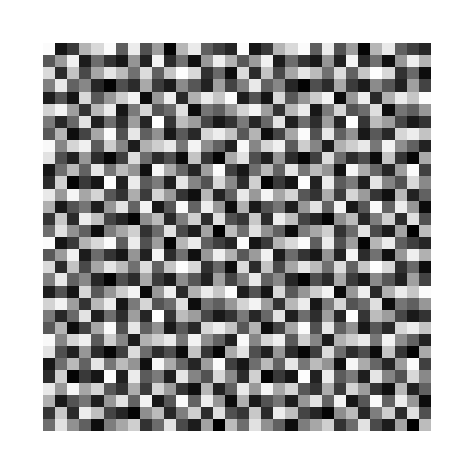

```mathematica
ArrayPlot[Join[Join[finalDist,finalDist],Join[finalDist,finalDist],2]]
```

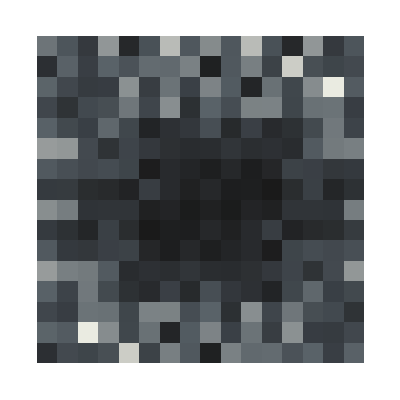

```mathematica
ArrayPlot[Abs[RotateLeft[Fourier[finalDist-0.5],{8,8}]],ColorFunction->"GrayTones"]
```

```mathematica
Convolve
```

```mathematica
finalDist2Vector={{{0.519444,0.430787},{0.94036,0.604582},{0.136051,0.933598},{0.768417,0.765048},{0.476575,0.580816},{0.735127,0.0823978},{0.947883,0.744003},{0.185367,0.689624},{0.595857,0.077371},{0.711087,0.829571},{0.95083,0.371572},{0.555808,0.0310745},{0.372489,0.69976},{0.254158,0.179917},{0.0860418,0.599345},{0.670646,0.00749567}},{{0.32096,0.00623767},{0.0210884,0.593488},{0.319716,0.388667},{0.695496,0.279704},{0.343685,0.914388},{0.1338,0.337367},{0.504128,0.361907},{0.541537,0.911524},{0.853208,0.585241},{0.475666,0.500984},{0.137552,0.0988023},{0.570744,0.877687},{0.607811,0.370296},{0.882298,0.917002},{0.584608,0.539685},{0.260077,0.877162}},{{0.539775,0.700926},{0.906721,0.187922},{0.844824,0.958392},{0.420928,0.105003},{0.707214,0.655164},{0.917461,0.261371},{0.100823,0.904086},{0.293766,0.0354781},{0.000705271,0.708442},{0.82093,0.190662},{0.128805,0.881162},{0.854812,0.524597},{0.186375,0.326874},{0.0859888,0.997248},{0.916206,0.402359},{0.634878,0.237737}},{{0.289515,0.291971},{0.163678,0.86093},{0.647548,0.509798},{0.144273,0.209434},{0.233115,0.703952},{0.968716,0.941437},{0.633509,0.15018},{0.63141,0.452538},{0.260199,0.307881},{0.640967,0.747011},{0.408107,0.187179},{0.765765,0.0331389},{0.74895,0.738358},{0.537171,0.215598},{0.159844,0.660211},{0.71829,0.910537}},{{0.763894,0.244516},{0.951578,0.564248},{0.569248,0.855797},{0.751494,0.0402213},{0.932372,0.491541},{0.301404,0.398025},{0.593026,0.835442},{0.963531,0.619577},{0.285555,0.871115},{0.00123374,0.49048},{0.968624,0.388761},{0.443713,0.626192},{0.26775,0.905721},{0.983236,0.226383},{0.502999,0.518875},{0.173362,0.0408018}},{{0.360261,0.664469},{0.0441827,0.378261},{0.496398,0.307573},{0.028116,0.892124},{0.296635,0.079263},{0.662544,0.277276},{0.0429294,0.76796},{0.390276,0.23285},{0.746325,0.0661838},{0.666276,0.544414},{0.211955,0.0657468},{0.670296,0.211445},{0.0455895,0.584416},{0.369694,0.155462},{0.995318,0.765216},{0.0383798,0.839799}},{{0.74366,0.70821},{0.429876,0.0612517},{0.938774,0.952894},{0.758436,0.439963},{0.677177,0.821359},{0.23532,0.858948},{0.794111,0.608807},{0.105287,0.0732006},{0.69112,0.919451},{0.42776,0.36209},{0.0760397,0.880454},{0.889423,0.697522},{0.581252,0.404848},{0.627564,0.908344},{0.690562,0.504839},{0.590197,0.175616}},{{0.838594,0.283763},{0.0184355,0.678756},{0.358637,0.784264},{0.682388,0.129352},{0.0279632,0.418804},{0.946668,0.0965927},{0.546907,0.439891},{0.554822,0.152766},{0.385799,0.724579},{0.872305,0.243487},{0.450859,0.112245},{0.00935972,0.214239},{0.338534,0.904729},{0.805919,0.132883},{0.268085,0.26728},{0.233583,0.869162}},{{0.0638022,0.113477},{0.937023,0.645149},{0.289637,0.289103},{0.669286,0.571303},{0.376855,0.125375},{0.270693,0.677177},{0.872021,0.927235},{0.046752,0.931941},{0.854334,0.551352},{0.071126,0.381849},{0.649319,0.702417},{0.99022,0.383073},{0.435282,0.533371},{0.142709,0.664623},{0.833663,0.899798},{0.512392,0.59605}},{{0.577357,0.944455},{0.537293,0.366672},{0.0939091,0.941222},{0.926197,0.254739},{0.415614,0.958793},{0.862828,0.493765},{0.272609,0.259233},{0.569957,0.7969},{0.285365,0.0426297},{0.688665,0.166525},{0.200408,0.895049},{0.599342,0.305403},{0.297344,0.0204257},{0.934242,0.638565},{0.491159,0.129527},{0.925625,0.0312776}},{{0.303601,0.0847153},{0.795,0.189821},{0.450837,0.657842},{0.810162,0.836983},{0.312126,0.37326},{0.655422,0.194787},{0.0481789,0.655964},{0.5436,0.311359},{0.991793,0.190022},{0.721371,0.597265},{0.679102,0.986419},{0.0187193,0.657786},{0.843819,0.222738},{0.119968,0.98326},{0.721912,0.539308},{0.324247,0.647565}},{{0.0344369,0.663832},{0.880728,0.482424},{0.459158,0.161253},{0.0711394,0.394396},{0.978181,0.00991647},{0.547589,0.617845},{0.980612,0.545397},{0.723423,0.910511},{0.157638,0.711773},{0.378678,0.333999},{0.0868492,0.0825771},{0.573067,0.531382},{0.683895,0.776158},{0.147227,0.324534},{0.575377,0.268762},{0.796699,0.820195}},{{0.153431,0.25417},{0.603043,0.762626},{0.181759,0.83294},{0.601912,0.443505},{0.658808,0.875305},{0.408903,0.102595},{0.267165,0.856999},{0.232533,0.168827},{0.744515,0.251048},{0.381705,0.930107},{0.897526,0.424056},{0.650047,0.14997},{0.104188,0.805568},{0.433153,0.0306593},{0.955828,0.164799},{0.272007,0.881776}},{{0.668061,0.272214},{0.841036,0.0175017},{0.953269,0.756305},{0.932418,0.27839},{0.0272413,0.897086},{0.232241,0.435204},{0.82436,0.128188},{0.602627,0.514709},{0.855969,0.626017},{0.381109,0.104078},{0.0369322,0.562734},{0.997939,0.786987},{0.331926,0.402456},{0.690981,0.488288},{0.927822,0.667175},{0.394217,0.203269}},{{0.00199748,0.814877},{0.662194,0.522616},{0.483088,0.90556},{0.262776,0.287951},{0.606009,0.283144},{0.616587,0.668045},{0.70496,0.975043},{0.429806,0.3194},{0.0336706,0.83157},{0.890292,0.986491},{0.629915,0.621903},{0.839003,0.128757},{0.597585,0.961039},{0.0932793,0.933657},{0.0662161,0.000106951},{0.345098,0.525813}},{{0.704657,0.97248},{0.238335,0.140215},{0.658233,0.11824},{0.127873,0.651251},{0.974751,0.473858},{0.264737,0.0914546},{0.172004,0.999706},{0.842717,0.347111},{0.173883,0.273313},{0.605555,0.322822},{0.206948,0.845629},{0.281722,0.34557},{0.860357,0.576756},{0.66678,0.235467},{0.615107,0.752722},{0.902189,0.350245}}};
```

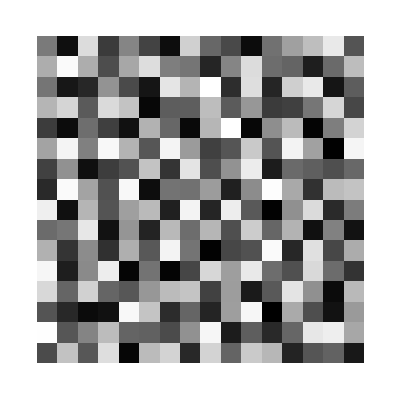

```mathematica
ArrayPlot[finalDist2Vector[[All,All,1]]]
```

-Graphics-

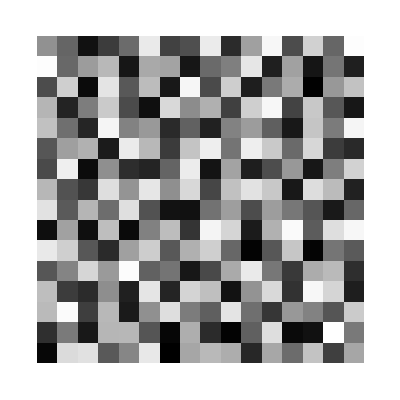

```mathematica
ArrayPlot[finalDist2Vector[[All,All,2]]]
```

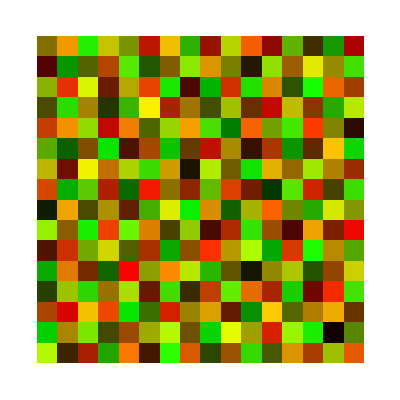

```mathematica
ArrayPlot[finalDist2Vector,ColorFunction->Function[x,RGBColor[x[[1]],x[[2]],0]]]
```

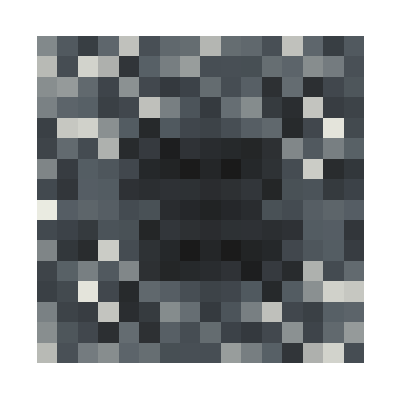

```mathematica
ArrayPlot[Abs[RotateLeft[Fourier[finalDist2Vector[[All,All,2]]-0.5],{8,8}]],ColorFunction->"GrayTones"]
```

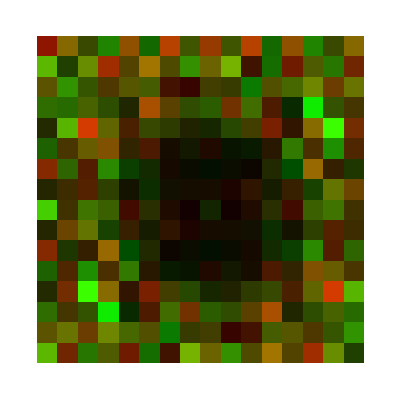

```mathematica
ArrayPlot[Abs[RotateLeft[Fourier[finalDist2Vector-0.5],{8,8}]],ColorFunction->Function[x,RGBColor[x[[1]],x[[2]],0]]]
```

```mathematica
finalDist3D={{{0.835384,0.751041,0.323277,0.234934,0.49521,0.755931,0.0081021,0.306291},{0.0962954,0.889642,0.658027,0.837435,0.57705,0.85768,0.620204,0.340806},{0.688533,0.360109,0.216599,0.962737,0.137057,0.540472,0.204699,0.480581},{0.223082,0.509932,0.0537544,0.779133,0.649262,0.104544,0.672217,0.891652},{0.72598,0.698516,0.621633,0.714093,0.825979,0.431575,0.78797,0.547716},{0.775077,0.349728,0.235469,0.40909,0.274191,0.760647,0.213682,0.958834},{0.1231,0.536644,0.791147,0.633811,0.908892,0.484808,0.68711,0.425183},{0.218285,0.46884,0.182842,0.443935,0.818413,0.392001,0.78183,0.714344}},{{0.433171,0.551753,0.694281,0.125332,0.262392,0.549111,0.668723,0.533834},{0.939731,0.269368,0.816761,0.426737,0.178582,0.470751,0.0576514,0.795555},{0.0304252,0.564622,0.489381,0.0211602,0.893796,0.350138,0.273282,0.76218},{0.857368,0.13495,0.949344,0.301187,0.0637461,0.70565,0.912465,0.399352},{0.195411,0.811014,0.172893,0.461041,0.222153,0.593174,0.157929,0.314777},{0.475775,0.565595,0.0999993,0.514344,0.141843,0.370334,0.861129,0.622688},{0.993026,0.91721,0.317275,0.675522,0.0184125,0.568875,0.0390179,0.27306},{0.500394,0.167637,0.978417,0.525389,0.342123,0.114208,0.897041,0.0826815}},{{0.869022,0.0103904,0.455276,0.956608,0.783584,0.292862,0.962807,0.127987},{0.604514,0.343706,0.197779,0.608146,0.401946,0.806246,0.644934,0.181338},{0.10731,0.420394,0.915518,0.105524,0.749853,0.000168211,0.843716,0.37157},{0.468609,0.783238,0.537303,0.381698,0.853738,0.627462,0.570419,0.99232},{0.283314,0.662458,0.0112535,0.572312,0.80061,0.473992,0.0915974,0.0196749},{0.893169,0.451284,0.735798,0.904329,0.307575,0.973717,0.698714,0.645894},{0.137611,0.0461188,0.275195,0.844663,0.616453,0.462353,0.349042,0.179488},{0.656063,0.801678,0.579898,0.748298,0.657629,0.824856,0.206765,0.744998}},{{0.236119,0.824484,0.151093,0.253993,0.073748,0.877677,0.339248,0.416349},{0.673341,0.555473,0.731691,0.481494,0.571982,0.22365,0.520655,0.895563},{0.222328,0.845155,0.653832,0.970068,0.67635,0.134841,0.311946,0.743615},{0.256111,0.303274,0.0710704,0.812549,0.522899,0.453199,0.827825,0.544712},{0.911484,0.832412,0.218367,0.687432,0.179686,0.26305,0.337385,0.712262},{0.104361,0.717391,0.154122,0.344277,0.555205,0.662552,0.524684,0.234106},{0.541898,0.377929,0.489717,0.105433,0.868736,0.122814,0.730603,0.83984},{0.280129,0.628327,0.0843437,0.417659,0.182083,0.860882,0.607794,0.453249}},{{0.763769,0.998579,0.368491,0.704571,0.637735,0.998491,0.00833591,0.504569},{0.0973463,0.466522,0.69177,0.142233,0.208528,0.445586,0.578558,0.803017},{0.634201,0.128526,0.437314,0.332364,0.794052,0.719403,0.943784,0.0451267},{0.761046,0.97725,0.499674,0.89048,0.0388894,0.0767746,0.229102,0.431458},{0.585315,0.169991,0.608119,0.279011,0.4867,0.636472,0.791024,0.142619},{0.323475,0.797485,0.0425245,0.961862,0.390393,0.811495,0.414467,0.481223},{0.577125,0.852198,0.445444,0.793466,0.760116,0.221849,0.944559,0.868154},{0.0637508,0.727632,0.895403,0.599606,0.510555,0.149814,0.561863,0.670674}},{{0.549095,0.178617,0.5755,0.786091,0.0624544,0.844458,0.242911,0.921768},{0.213307,0.715712,0.0498815,0.273789,0.916013,0.683596,0.125699,0.301217},{0.657366,0.396715,0.623304,0.829199,0.464963,0.75782,0.536796,0.841873},{0.489891,0.904107,0.0318257,0.543862,0.402332,0.174313,0.886528,0.00768543},{0.939332,0.369126,0.824449,0.707537,0.120831,0.316662,0.690536,0.262562},{0.659252,0.0148355,0.342114,0.646384,0.749859,0.547051,0.030702,0.734467},{0.222915,0.915568,0.552879,0.202675,0.907286,0.829106,0.273451,0.108984},{0.352267,0.121862,0.302619,0.658187,0.0106332,0.425333,0.0460833,0.787693}},{{0.868688,0.264462,0.5176,0.883647,0.356638,0.606362,0.328506,0.655337},{0.823834,0.451707,0.968008,0.18933,0.551909,0.778399,0.161382,0.738798},{0.155531,0.793799,0.746619,0.109716,0.643637,0.291383,0.361884,0.420766},{0.332664,0.675958,0.309049,0.786698,0.217711,0.595761,0.510931,0.773703},{0.204405,0.469095,0.259533,0.508404,0.858464,0.905092,0.244623,0.8224},{0.531861,0.616583,0.739259,0.0727206,0.798758,0.455781,0.167309,0.677046},{0.709535,0.0574769,0.15873,0.474729,0.129373,0.287321,0.991295,0.891373},{0.480247,0.429521,0.84729,0.219873,0.535854,0.699575,0.406381,0.180881}},{{0.149411,0.607591,0.906159,0.721037,0.146226,0.254699,0.950896,0.514912},{0.379955,0.00545921,0.0753532,0.41029,0.807111,0.0329646,0.444583,0.879614},{0.25387,0.593132,0.865541,0.687179,0.321353,0.729379,0.0855122,0.571666},{0.920866,0.555618,0.416995,0.165319,0.482865,0.976893,0.131421,0.630985},{0.0626933,0.143028,0.880357,0.00189618,0.353092,0.562404,0.0114785,0.345139},{0.274564,0.975247,0.57351,0.95212,0.662667,0.0573367,0.841239,0.445222},{0.815671,0.384652,0.830472,0.603111,0.175093,0.583955,0.337159,0.0726896},{0.630888,0.687586,0.104967,0.0386912,0.85015,0.735137,0.0973876,0.57447}}};
```

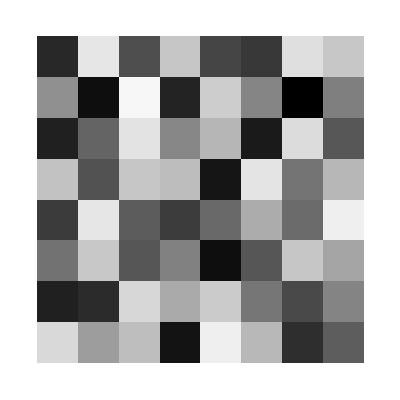

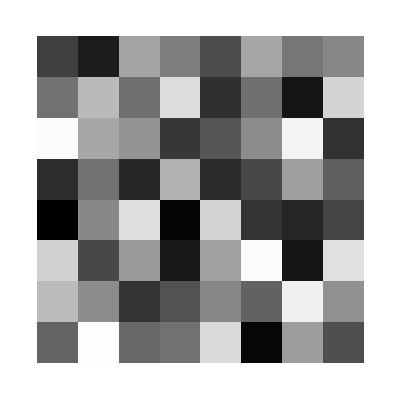

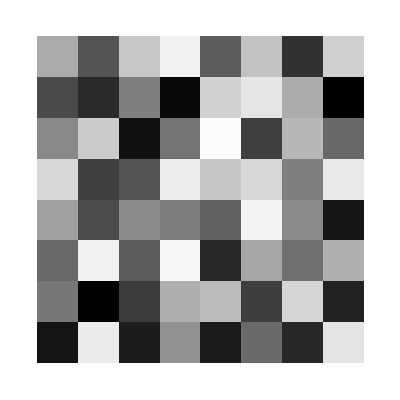

```mathematica
ArrayPlot[finalDist3D[[All,All,1]]]
ArrayPlot[finalDist3D[[All,All,2]]]
ArrayPlot[finalDist3D[[All,All,3]]]
```

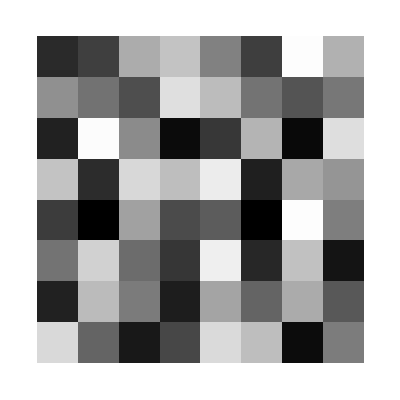

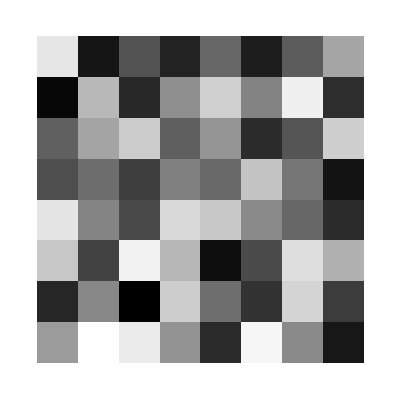

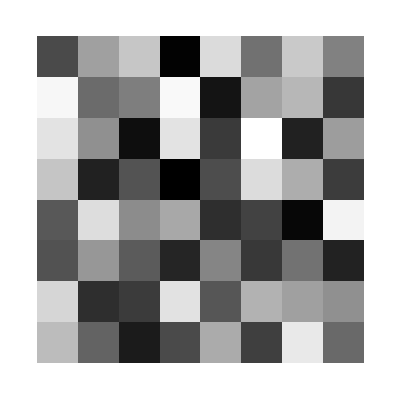

```mathematica
ArrayPlot[finalDist3D[[All,1,All]]]
ArrayPlot[finalDist3D[[All,2,All]]]
ArrayPlot[finalDist3D[[All,3,All]]]
```

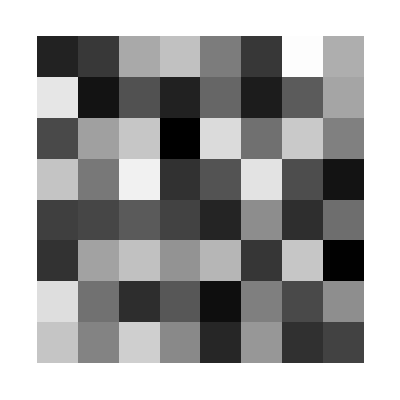

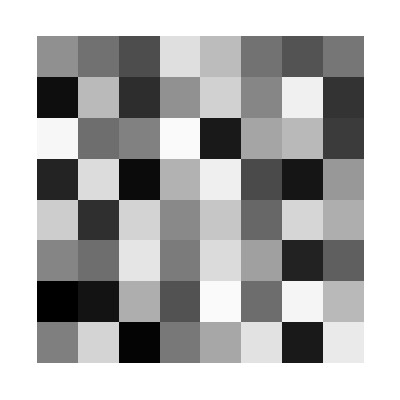

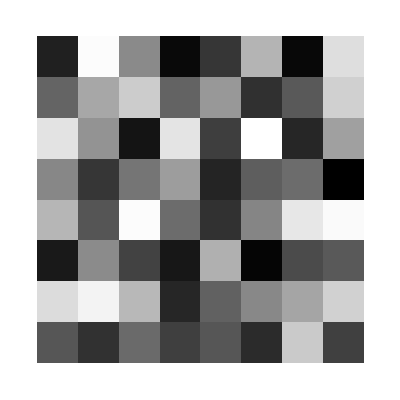

```mathematica
ArrayPlot[finalDist3D[[1,All, All]]]
ArrayPlot[finalDist3D[[2,All, All]]]
ArrayPlot[finalDist3D[[3,All, All]]]
```